## Transforming the Bounding Boxes

Discovery: The Calbirds dataset bboxes are in the COCO format.

Need: {x_min, y_min, width, height} ⟶ Normalized[{x_center, y_center, width, height}]

#### Discovery:

Resize Image: 416, 416
Bbox format: 
	- pascal: {x_min, y_min, x_max, y_max}
	- yolo: {x_center, y_center, width, height}

```mathematica
phase = "test";
inames = FileNames["*.jpg", "C:\\Users\\adamd\\OneDrive\\Documents\\AI Camp\\"<>phase<>"\\images"];
bnames = FileNames["*.txt", "C:\\Users\\adamd\\OneDrive\\Documents\\AI Camp\\"<>phase<>"\\labels"];
images = Import/@inames;
bboxes = Import/@bnames;
```

```mathematica
im = images[[-7]];
bbox = bboxes[[-7]];
Information@im
bbox
```

Image

0 110.0 103.0 183.0 169.0

### Exploration

#### Pascal: {x_min, y_min, x_max, y_max}

```mathematica
dims = ImageDimensions[im];
bbox = Partition[ToExpression/@StringSplit[box][[2;;]],2];
verticalReflection[coords_, ydim_]:= {{coords[[1,1]], ydim - coords[[2, 2]]}, {coords[[2,1]], ydim - coords[[1,2]]}};
{mins, maxs} = verticalReflection[bbox,dims[[2]]];
HighlightImage[im, Rectangle[mins, maxs]]
```

-Graphics-

#### COCO: {x_min, y_min, width, height}

```mathematica
processFormat[bbox_] := Partition[ToExpression/@StringSplit[bbox][[2;;]],2];
pascal2COCO[bbox_] := {bbox[[1]], {bbox[[2,1]]+bbox[[1,1]], bbox[[2,2]]+bbox[[1,2]]}};
verticalReflection[coords_, ydim_]:=
{{coords[[1,1]], ydim - coords[[2, 2]]}, {coords[[2,1]], ydim - coords[[1,2]]}};
transformBboxCOCO[bbox_, ydim_] := 
verticalReflection[#,ydim]&@pascal2COCO@processFormat@bbox
```

```mathematica
dims = ImageDimensions[im];
box = transformBboxCOCO[bbox, dims[[2]]];
HighlightImage[im, Rectangle@@box]
```

-Graphics-

#### Yolo: {x_center, y_center, width, height}; normalized

```mathematica
inames[[1]];
bnames[[1]];
yoloImage = images[[1]];
yoloBbox = bboxes[[1]];
dims = ImageDimensions@yoloImage;
```

```mathematica
labelStr2Num[bbox_] := ToExpression/@StringSplit[bbox][[2;;]];
processFormat[bbox_] := Partition[labelStr2Num@bbox,2];
mins[bbox_] := {bbox[[1,1]] - bbox[[2,1]]/2, bbox[[1,2]] - bbox[[2,2]]/2}
maxs[bbox_] := {bbox[[1,1]] + bbox[[2,1]]/2,  bbox[[1,2]] + bbox[[2,2]]/2}
yolo2Pascal[bbox_] := {mins[bbox], maxs[bbox]}
verticalReflection[coords_, ydim_]:={{coords[[1,1]], ydim - coords[[2, 2]]}, {coords[[2,1]], ydim - coords[[1,2]]}};
transformBboxYolo[bbox_, ydim_] := verticalReflection[#,ydim]&@yolo2Pascal@(ydim*processFormat@bbox)
```

```mathematica
HighlightImage[yoloImage, Rectangle@@transformBboxYolo[yoloBbox, dims[[2]]]]
```

-Graphics-

### Processing Pascal (Wolfram) ⟶ Yolo

And I’ll check with my Yolo transform function

1. transformBboxCOCO[bbox]

#### Read Data

```mathematica
phase = "test";
inames = FileNames["*.jpg", "C:\\Users\\adamd\\OneDrive\\Documents\\AI Camp\\"<>phase<>"\\images"];
bnames = FileNames["*.txt", "C:\\Users\\adamd\\OneDrive\\Documents\\AI Camp\\"<>phase<>"\\labels"];
images = Import/@inames;
bboxes = Import/@bnames;
removeInvalidData[data_]:=Select[data, Length[StringSplit[#[[2]]]]<=5 &&Length[StringSplit[#[[2]]]]>0&];
data = removeInvalidData@Transpose[{images, bboxes}];
Length@data
```

98

#### Define Helpers

```mathematica
(*HELPERS*)
labelStr2Num[bbox_] := ToExpression/@StringSplit[bbox][[2;;]];
processFormat[bbox_] := Partition[labelStr2Num@bbox,2];
mins[bbox_] := {bbox[[1,1]] - bbox[[2,1]]/2, bbox[[1,2]] - bbox[[2,2]]/2}
maxs[bbox_] := {bbox[[1,1]] + bbox[[2,1]]/2,  bbox[[1,2]] + bbox[[2,2]]/2}
verticalReflection[coords_, ydim_]:={{coords[[1,1]], ydim - coords[[2, 2]]}, {coords[[2,1]], ydim - coords[[1,2]]}};
yolo2pascal[bbox_] := {mins[bbox], maxs[bbox]}
coco2pascal[bbox_] := {bbox[[1]], {bbox[[2,1]]+bbox[[1,1]], bbox[[2,2]]+bbox[[1,2]]}};
getYdim[ex_] := (ImageDimensions@ex[[1]])[[2]];
isYolo[ex_] :=Total@labelStr2Num[ex[[2]]] < 4;
transformBboxYolo[bbox_, ydim_] := yolo2pascal @(ydim*processFormat@bbox)
transformBboxCOCO[bbox_, ydim_] := coco2pascal@processFormat@bbox

(*WORKING FUNCTIONS*)
processExample[ex_ /;isYolo[ex]] := {ex[[1]],transformBboxYolo[ex[[2]], getYdim[ex]]}; (*YOLO*)
processExample[ex_ /;!isYolo[ex]] := {ex[[1]],transformBboxCOCO[ex[[2]], getYdim[ex]]}; (*COCO*)
showBbox[im_, box_] := HighlightImage[im, Rectangle@@verticalReflection[#,getYdim[{im, box}]]&@box]
```

#### Process Data (⟶ Pascal)

```mathematica
pdata := processExample /@ data;
Length@pdata
Row[showBbox@@@pdata[[5;;10]]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Transform Data (Resizing to 416x416)

{x_min, y_min, x_max, y_max} ⟶ {x_center, y_center, width, height}

```mathematica
padSize[x_]:= ({416,416} - ImageDimensions@x[[1]])/2
restrictRange[coord_] := ((HeavisideTheta[#] - HeavisideTheta[#-416])*# + 416*HeavisideTheta[#-416])& @ coord
padShift[x_] := Partition[restrictRange/@Flatten@(Plus[padSize[x], #]&/@x[[2]]),2]
resizeX[x_] := {ImageCrop[x[[1]], {416, 416}, Center], padShift[x]}

Row[showBbox@@@x]
xnew = Row[showBbox@@@resizeX/@x]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

What restrictRange does:

```mathematica
restrictRange[coord_] := ((HeavisideTheta[#] - HeavisideTheta[#-416])*# + 416*HeavisideTheta[#-416])& @ coord
```

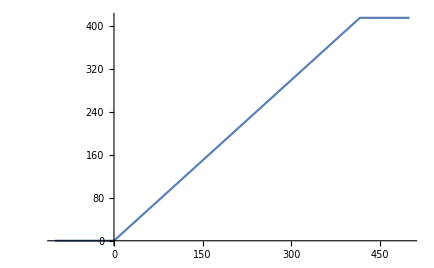

```mathematica
Plot[restrictRange[x], {x, -100, 500}, Axes->{True, False}]
```

#### Transform to Yolo

```mathematica
centers[box_] := Mean/@Transpose@box
boxdims[box_]:= Subtract@@@Minus/@Transpose@box
transformPascal2Yolo[x_] := {x[[1]],{centers[x[[2]]],boxdims[x[[2]]]}/416}
```

Verify with Yolo ⟶ Pascal

Does my Pascal ⟶ Yolo ⟶ Pascal pipeline work?

```mathematica
transformBboxYolo[bbox_] := yolo2pascal @(416*bbox)
transformBboxYolo[transformPascal2Yolo[x[[3]]][[2]]] == x[[3,2]]
```

True

#### Writing data into file system

```mathematica
box2str[box_] := StringJoin[Riffle[Prepend[ToString/@Flatten@box, "0"]," "]]
iname[i_, stage_] := StringJoin[{"C:\\Users\\adamd\\OneDrive\\Documents\\birds-dataset\\",stage,"\\images\\",stage,"_bird",ToString[i],".jpg"}]
fname[i_, stage_] := StringJoin[{"C:\\Users\\adamd\\OneDrive\\Documents\\birds-dataset\\",stage,"\\labels\\",stage,"_bird",ToString[i],".txt"}]

writeData[finaldata_, phase_]:=Module[{n=1, stage=phase}, 
While[n<=Length[finaldata],
datum := finaldata[[n]];

fileJpg := iname[n,stage];
Export[fileJpg, datum[[1]]];

fileTxt := fname[n, stage];
CreateFile[fileTxt];
WriteString[fileTxt, datum[[2]]];
Close[fileTxt];
n++;
]
];
```

```mathematica
newdata:=transformPascal2Yolo/@resizeX/@pdata
finaldata := {#[[1]],box2str[#[[2]]]}& /@ newdata
writeData[finaldata, phase]
```

### Full pipeline

```mathematica
phase = "train";
inames = FileNames["*.jpg", "C:\\Users\\adamd\\OneDrive\\Documents\\AI Camp\\"<>phase<>"\\images"];
bnames = FileNames["*.txt", "C:\\Users\\adamd\\OneDrive\\Documents\\AI Camp\\"<>phase<>"\\labels"];
images = Import/@inames;
bboxes = Import/@bnames;
removeInvalidData[data_]:=Select[data, Length[StringSplit[#[[2]]]]<=5 &&Length[StringSplit[#[[2]]]]>0&];
data = removeInvalidData@Transpose[{images, bboxes}];
pdata := processExample /@ data;
newdata:=transformPascal2Yolo/@resizeX/@pdata
finaldata := {#[[1]],box2str[#[[2]]]}& /@ newdata
writeData[finaldata, phase]
```